```mathematica
Tm=1356; (*melting temperature*)
dT=50; (* transition zone *)
dH=205000; (*latent heat*)
CpS=380; (*Heat capacity solid *)
(*CpL=530;*) (*Heat capacity liq*)
```

#### These are the values for the TiAl4V which are used in the modeling of the steady state :

```mathematica
Clear[CpL]
```

```mathematica
Tm=1877.15; (*melting temperature*)
Tl = 1923.15; (* liquidus *)
dT=10(Tl-Tm); (* transition zone *)
dH=0.1*2.86 10^11; (*latent heat*)


Clear[CpS]
CpS=ImportString["5.459e+08,300.129
5.73401e+08,428.341
6.04149e+08,556.591
6.28414e+08,670.555
6.52667e+08,798.729
6.83409e+08,934.084
7.07674e+08,1048.05
7.31927e+08,1176.22
6.88044e+08,1225.44
6.42538e+08,1274.63
6.66768e+08,1431.22
6.95869e+08,1587.87
7.23341e+08,1751.61
7.55673e+08,1929.61
7.99515e+08,1930.13
8.30362e+08,1937.6
8.49842e+08,1944.94
8.48051e+08,2150.95
8.47872e+08,2371.2
8.47716e+08,2563.03
8.45931e+08,2761.94
8.45764e+08,2967.98
8.45602e+08,3166.91
8.45487e+08,3309.01","Data"]; (*Heat capacity solid is a list*)
CpL = 8.45487 10^8;(*Heat capacity liq is a list*)
```

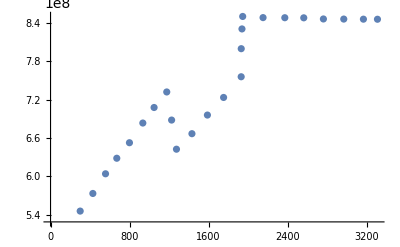

```mathematica
CpS[[All,{1,2}]] = CpS[[All,{2,1}]];
ListPlot[CpS]
```

```mathematica
CpL
```

8.45487×10^8

```mathematica
ufun=ListInterpolation[CpS[[All,2]],{{400,2400}}]
```

InterpolatingFunction[…]

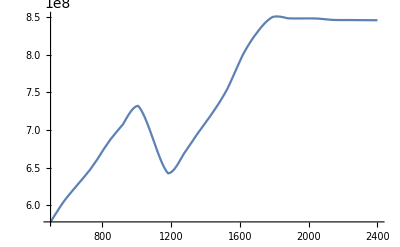

```mathematica
Plot[ufun[x],{x,500,2400}]
```

```mathematica
α[t_]:=1/2( 1+Tanh[4/dT*(t-Tm)]);
dα[t_]=D[α[t],t]
Cp[t_]:=ufun[t]*(1-α[t])+CpL*α[t]+dH*dα[t];
```

0.00434783 Sech[0.00869565 (-1877.15+t)]^2

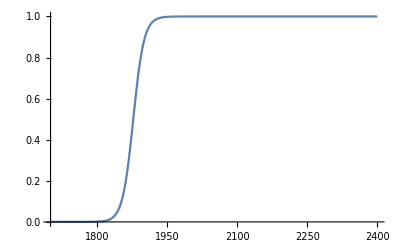

```mathematica
Plot[α[t],{t,1700,2400}]
```

```mathematica
N@Cp[1400]
```

7.09403×10^8

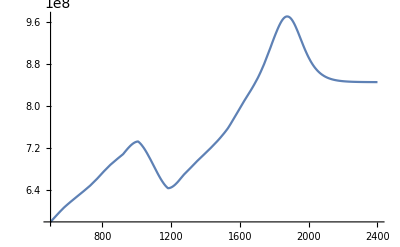

```mathematica
Plot[Cp[t],{t,500,2400},PlotRange->All]
```

```mathematica
CpL
```

530

```mathematica
TiAl4Vtable=Table[{N@Cp[t],t},{t,500,2400,15}]
```

{{5.78044×10^8,500},{5.83431×10^8,515},{5.88821×10^8,530},{5.94165×10^8,545},{5.99412×10^8,560},{6.04479×10^8,575},{6.08934×10^8,590},{6.13232×10^8,605},{6.17406×10^8,620},{6.21489×10^8,635},{6.25514×10^8,650},{6.29515×10^8,665},{6.33524×10^8,680},{6.37575×10^8,695},{6.41702×10^8,710},{6.45937×10^8,725},{6.50315×10^8,740},{6.55135×10^8,755},{6.60405×10^8,770},{6.6577×10^8,785},{6.71163×10^8,800},{6.76518×10^8,815},{6.81768×10^8,830},{6.86471×10^8,845},{6.90826×10^8,860},{6.95045×10^8,875},{6.9916×10^8,890},{7.03204×10^8,905},{7.0721×10^8,920},{7.13065×10^8,935},{7.18858×10^8,950},{7.23992×10^8,965},{7.28117×10^8,980},{7.30884×10^8,995},{7.31606×10^8,1010},{7.26884×10^8,1025},{7.20505×10^8,1040},{7.12812×10^8,1055},{7.04144×10^8,1070},{6.94845×10^8,1085},{6.85215×10^8,1100},{6.75545×10^8,1115},{6.663×10^8,1130},{6.57845×10^8,1145},{6.50547×10^8,1160},{6.44772×10^8,1175},{6.42802×10^8,1190},{6.44716×10^8,1205},{6.48207×10^8,1220},{6.52945×10^8,1235},{6.58595×10^8,1250},{6.64825×10^8,1265},{6.70152×10^8,1280},{6.75093×10^8,1295},{6.80123×10^8,1310},{6.85211×10^8,1325},{6.90324×10^8,1340},{6.95428×10^8,1355},{7.00165×10^8,1370},{7.04852×10^8,1385},{7.09561×10^8,1400},{7.14328×10^8,1415},{7.1919×10^8,1430},{7.24182×10^8,1445},{7.29341×10^8,1460},{7.34708×10^8,1475},{7.40328×10^8,1490},{7.46243×10^8,1505},{7.52499×10^8,1520},{7.59419×10^8,1535},{7.67347×10^8,1550},{7.75569×10^8,1565},{7.83992×10^8,1580},{7.92529×10^8,1595},{8.01104×10^8,1610},{8.09282×10^8,1625},{8.17096×10^8,1640},{8.25013×10^8,1655},{8.33158×10^8,1670},{8.41668×10^8,1685},{8.50701×10^8,1700},{8.60635×10^8,1715},{8.71447×10^8,1730},{8.83104×10^8,1745},{8.95595×10^8,1760},{9.08788×10^8,1775},{9.22374×10^8,1790},{9.35171×10^8,1805},{9.472×10^8,1820},{9.57682×10^8,1835},{9.65665×10^8,1850},{9.70281×10^8,1865},{9.71002×10^8,1880},{9.67924×10^8,1895},{9.61081×10^8,1910},{9.51286×10^8,1925},{9.39601×10^8,1940},{9.27104×10^8,1955},{9.1472×10^8,1970},{9.03121×10^8,1985},{8.92719×10^8,2000},{8.83698×10^8,2015},{8.76079×10^8,2030},{8.69773×10^8,2045},{8.64636×10^8,2060},{8.60503×10^8,2075},{8.57214×10^8,2090},{8.54616×10^8,2105},{8.52575×10^8,2120},{8.50981×10^8,2135},{8.4974×10^8,2150},{8.48776×10^8,2165},{8.48028×10^8,2180},{8.47449×10^8,2195},{8.47002×10^8,2210},{8.46655×10^8,2225},{8.46388×10^8,2240},{8.46182×10^8,2255},{8.46022×10^8,2270},{8.459×10^8,2285},{8.45805×10^8,2300},{8.45732×10^8,2315},{8.45676×10^8,2330},{8.45632×10^8,2345},{8.45599×10^8,2360},{8.45573×10^8,2375},{8.45554×10^8,2390}}

```mathematica
Export["C:\\Users\\tonii\\OneDrive\\Documents\\GitHub\\Mathematica\\TiAl4VValues.csv",TiAl4Vtable];
```

```mathematica
Clear[Tm,dT,dH,CpS,CpL];
Tm=1288; Ts=1188;
(*melting temperature*)
dT=50; (* transition zone *)
dH=60; (*latent heat*)
CpS=0.396; (*Heat capacity solid *)
CpL=0.49; (*Heat capacity liq*)
```

```mathematica
Plot[Cp[t],{t,1000,1250},PlotRange->{All,{0,7}},Frame->True]
```

-Graphics-

```mathematica
Export["C:\\Users\\tonii\\OneDrive\\Documents\\GitHub\\Mathematica\\BronzeValues.csv",Table[{N@Cp[t]*10^9,t},{t,1150,1230,5}]]
```

C:\Users\tonii\OneDrive\Documents\GitHub\Mathematica\BronzeValues.csv

```mathematica
(*function used in abaqus to smooth transition from solid to liq*)
ζ[t_]:=(t-Ts)/(Tm-Ts)
Ut[θ_]:=(ζ[θ])^3(10-15 ζ[θ]+6 ζ[θ]^2)
dUt[θ_]=D[Ut[θ],θ]
```

(3 (10-3/20 (-1188+θ)+(3 (-1188+θ)^2)/5000) (-1188+θ)^2)/1000000+((-3/20+(3 (-1188+θ))/2500) (-1188+θ)^3)/1000000

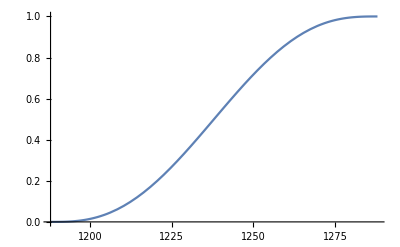

```mathematica
Plot[Ut[θ],{θ,1188,1288}]
```

```mathematica
Cp[t_]:=CpS(1-Ut[t])+CpL Ut[t]+dH dUt[t];
```

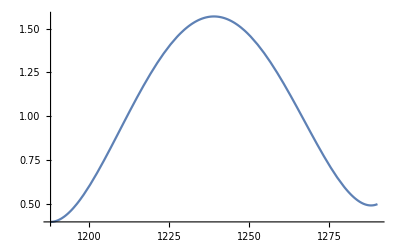

```mathematica
Plot[Cp[t],{t,1188,1290}]
```

```mathematica
Export["C:\\Users\\tonii\\OneDrive\\Documents\\GitHub\\Mathematica\\BronzeValues.csv",Table[{N@Cp[t]*10^9,t},{t,1188,1288,5}]]
```

C:\Users\tonii\OneDrive\Documents\GitHub\Mathematica\BronzeValues.csv

```mathematica
Mean[{0.45,0.11,0.08}]
```

0.213333

```mathematica
Clear[Tm,dT,dH,CpS,CpL];
Tm=1; Ts=0.95; 
(*melting temperature*)
dT=0.1; (* transition zone *)
dH=1; (*latent heat*)
CpS=1; (*Heat capacity solid *)
CpL=1;
```

```mathematica
α[t_]:=1/2( 1+Tanh[4/dT*(t-Tm)]);
dα[t_]=D[α[t],t]
Cp[t_]:=CpS*(1-α[t])+CpL*α[t]+dH*dα[t];
```

20. Sech[40. (-1+t)]^2

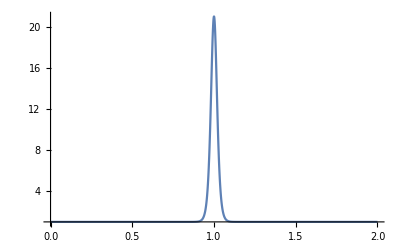

```mathematica
Plot[Cp[t],{t,0,2},PlotRange->All]
```

```mathematica
Export["C:\\Users\\tonii\\OneDrive\\Documents\\GitHub\\Mathematica\\freezingsolid_appHeat.csv",Table[{N@Cp[t],t},{t,0,2,0.05}]]
```

C:\Users\tonii\OneDrive\Documents\GitHub\Mathematica\freezingsolid_appHeat.csv